### Classical Skyrmion Profiles

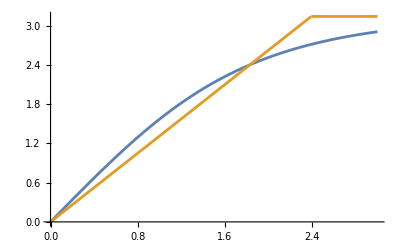

```mathematica
w=1;(* sharpness of the domain wall *)
R=1;(* radius of the profile *)
L=3R;(* size of the cluster *)
μ=1.;(* winding number *)
ϕ0=-π/2;(* helicity *)
dr0 = D[θsk[r],r]/.r->R;
Clear[θsk]
Clear[θsk2]
θsk[r_]:=2ArcTan[Sinh[r/w]/Sinh[R/w]](* single skyrmion profile *)
θsk2[r_]:=π Clip[dr0(r/R)/π,{10^-12,1-10^-12}](* single skyrmion profile *)
Plot[{θsk[r],θsk2[r]},{r,0,L},PlotRange->Full]
HueVlad[spec_]:=Blend[{Black,Hue[0.5+spec[[1]]],White},spec[[2]]]
m[θ_,ϕ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]}/2
M[θ_,ϕ_,csq_]:=m[θ,-ϕ]+csq(m[θ,ϕ]-m[θ,-ϕ])
Φ[ϕ_]:=Clip[Mod[μ ϕ + ϕ0,2π]-π,{-π+10^-12,π-10^-12}]
```

```mathematica
xs=Table[x,{x,-L+10^-8,L-10^-8,L/8}];
ys=xs;
listCart=Flatten[Table[{x0={x,y,0}-0.(mm=m[θsk[Norm[{x,y}]],Φ[ArcTan[x,y]]]),x0+mm,{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),1-2mm[[3]]}},{x,xs},{y,ys}],1];
listSp=Flatten[Table[{x0=FromSphericalCoordinates[{1,θsk[Norm[{x,y}]],ArcTan[x,y]}],x0+(mm=m[θsk[Norm[{x,y}]],Φ[ArcTan[x,y]]]),{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),1-2mm[[3]]}},{x,xs},{y,ys}],1];
light =Automatic;
skCart=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.03],Arrow[Tube[#[[;;2]]]]}&/@listCart,ViewPoint->Top,Boxed->False,Lighting->light];
skSph=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.05],Arrow[Tube[#[[;;2]]]]}&/@listSp,Lighting->light];
skSph=Show[Graphics3D[{Opacity[0.1],Sphere[]}],skSph,ViewPoint->Top,Boxed->False,Lighting->light];
listCart=Flatten[Table[{x0={x,y,0}-0.(mm=m[θsk[Norm[{x,y}]],-Φ[ArcTan[x,y]]]),x0+mm,{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),1-2mm[[3]]}},{x,xs},{y,ys}],1];
listSp=Flatten[Table[{x0=FromSphericalCoordinates[{1,θsk[Norm[{x,y}]],ArcTan[x,y]}],x0+(mm=m[θsk[Norm[{x,y}]],-Φ[ArcTan[x,y]]]),{(ArcTan[mm[[1]],mm[[2]]]+π)/(2π),1-2mm[[3]]}},{x,xs},{y,ys}],1];

askCart=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.03],Arrow[Tube[#[[;;2]]]]}&/@listCart,ViewPoint->Top,Boxed->False,Lighting->light];
askSph=Graphics3D[{HueVlad[#[[3]]],Arrowheads[.05],Arrow[Tube[#[[;;2]]]]}&/@listSp,Lighting->light];
askSph=Show[Graphics3D[{Opacity[0.1],Sphere[]}],askSph,ViewPoint->Top,Boxed->False,Lighting->light];
im2=GraphicsGrid[{{skCart,askCart},{skSph,askSph}}]
```

-Graphics-

{ConditionalExpression[π-1/2 ArcCos[-Cot[θ]^2], π/4≤θ≤(3 π)/4],ConditionalExpression[-1/2 ArcCos[-Cot[θ]^2], π/4≤θ≤(3 π)/4],ConditionalExpression[1/2 ArcCos[-Cot[θ]^2], π/4≤θ≤(3 π)/4],ConditionalExpression[1/4 (-3 π+2 ArcSin[Cot[θ]^2]), π/4≤θ≤(3 π)/4]}

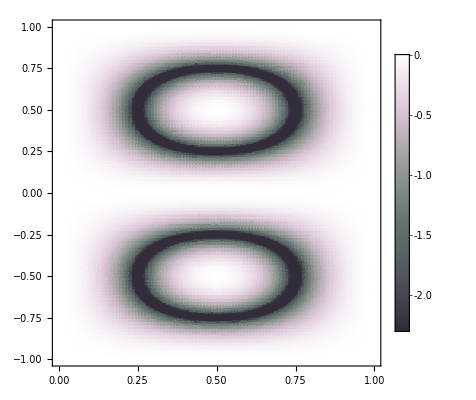

```mathematica
(* orthogonality between skyrmion and anti-skyrmion *)
clip=Log[10^-1];
$Assumptions=0<θ<=π&&-π<ϕ<=π;
solutions =ϕ/. FullSimplify[Solve[m[θ,ϕ].m[θ,-ϕ]==0,ϕ]]
DensityPlot[Log[Abs[4m[θ π,ϕ π].m[θ π,-ϕ π]]],{θ,10^-12,1},{ϕ,-1+10^-12,1},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,0}]]&),ColorFunctionScaling->False,PlotRange->{clip,0},ClippingStyle->Black,PlotRange->Full, GridLines->{{1/4,3/4},{}},GridLinesStyle->{{Dashed,Black},{}},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

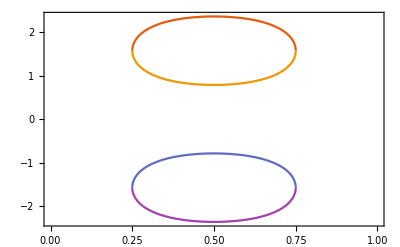

```mathematica
<<MaTeX`
Plot[Evaluate@(solutions/.{θ->x π}),{x,1/4,3/4}, GridLines->{{1/4,3/4},{}},PlotTheme->"Scientific",PlotRange->{{0,1},Full},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

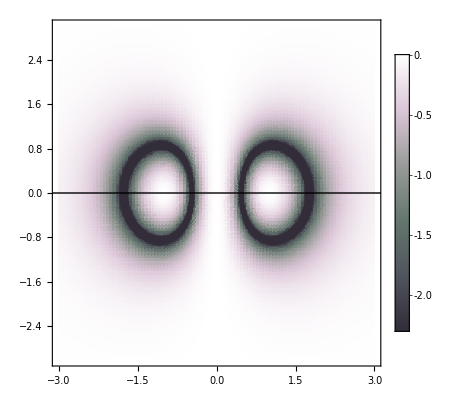

```mathematica
(* orthogonality between skyrmion and anti-skyrmion magnetization in real-space *)
clip=Log[10^-1];
overlap=DensityPlot[Log[Abs[4m[θsk[Norm[{x,y}]] ,Φ[ArcTan[x,y]]].m[θsk[Norm[{x,y}]] ,-Φ[ArcTan[x,y]]]]],{x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,0}]]&),ColorFunctionScaling->False,PlotRange->{clip,0},ClippingStyle->Black,GridLines->None,GridLinesStyle->{{Dashed,Black},{}},ClippingStyle->Red,FrameLabel->MaTeX[{"x","y"}],Exclusions->None];
Show[overlap,Graphics[Line[{-2L{Sin[ϕ0],Cos[ϕ0]},2L{Sin[ϕ0],Cos[ϕ0]}}]]]
```

```mathematica
Show[{skCart,askCart}]
```

-Graphics3D-

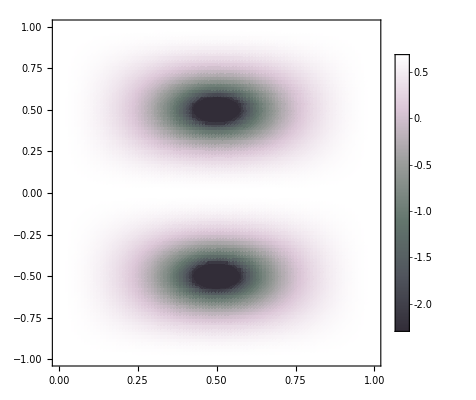

```mathematica
(* orthogonality between quantum skyrmion and quantum anti-skyrmion *)
$Assumptions=0<θ<=π&&-π<ϕ<=π;
clip=Log[10^-1];
qoverlap=DensityPlot[Log[4m[θ π,ϕ π].m[θ π,-ϕ π]+1],{θ,10^-12,1},{ϕ,-1+10^-12,1},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,Log[2]}]]&),ColorFunctionScaling->False,PlotRange->{clip,Log[2]},ClippingStyle->Black,PlotRange->Automatic, GridLines->{{1/4,1/2,3/4},{-0.5,0.5}},GridLinesStyle->{{Dashed,Black},{Dashed,Black}},FrameLabel->MaTeX[{"\\theta","\\phi"}]]
```

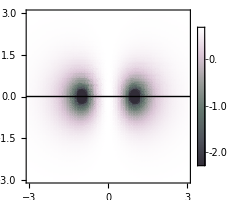

```mathematica
(* orthogonality between quantum skyrmion and anti-skyrmion wave function in real-space *)
clip=Log[10^-1];
overlap=DensityPlot[Log[4m[θsk[Norm[{x,y}]] ,Φ[ArcTan[x,y]]].m[θsk[Norm[{x,y}]] ,-Φ[ArcTan[x,y]]]+1],{x,-L,L},{y,-L,L},PlotLegends->Automatic,PlotPoints->100,PlotTheme->"Scientific",ColorFunction->(ColorData["PigeonTones"][Rescale[#,{clip,Log[2]}]]&),ColorFunctionScaling->False,PlotRange->{clip,Log[2]},ClippingStyle->Black,GridLines->None,GridLinesStyle->{{Dashed,Black},{}},ClippingStyle->Red,FrameLabel->MaTeX[{"x","y"}],Exclusions->None];
Show[overlap,Graphics[Line[{-2L{Sin[ϕ0],Cos[ϕ0]},2L{Sin[ϕ0],Cos[ϕ0]}}]],ImageSize->200]
```

### Classical Product state

```mathematica
dn={0,1};
S={sx,sy,sz} = Table[PauliMatrix[i]/2,{i,3}];
```

```mathematica
Clear[R]
R[θ_,ϕ_]:=MatrixExp[-ⅈ sz ϕ].MatrixExp[-ⅈ sy (θ-π)]
sk=R[θ,ϕ].dn;
ask=R[θ,-ϕ].dn;
Table[sk†.s.sk,{s,S}]-m[θ,ϕ]//FullSimplify
Table[ask†.s.ask,{s,S}]-m[θ,-ϕ]//FullSimplify
```

{0,0,0}

{0,0,0}

```mathematica
(* for each spin, the overlap is given by a product of the kind *)
ovl=sk†.ask//FullSimplify
```

Cos[ϕ]+ⅈ Cos[θ] Sin[ϕ]

```mathematica
$Assumptions=-π<ϕ<=π&&0<θ<π;
√(Re[ovl]^2+Im[ovl]^2)//FullSimplify
```

√(Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2)

```mathematica
ovl**ovl//FullSimplify
```

Cos[ϕ]^2+Cos[θ]^2 Sin[ϕ]^2

```mathematica
ovl**ovl-(2m[θ,ϕ].m[θ,-ϕ]+1/2)//TrigExpand//FullSimplify
```

0

```mathematica
4m[θ,ϕ].m[θ,-ϕ]+1//FullSimplify
```

1/2 (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

```mathematica
2m[θ,ϕ].m[θ,-ϕ]-(Re[ovl]^2+Im[ovl]^2)//FullSimplify
```

-1/2

```mathematica
2M[θ,ϕ,c]//FullSimplify
```

{Cos[ϕ] Sin[θ],(-1+2 c) Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
M[θ,ϕ,c].M[θ,ϕ,c]//ExpandAll//FullSimplify
```

1/4 (Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))

```mathematica
Grad[M[θ,ϕ,c].M[θ,ϕ,c],{θ,ϕ}]//FullSimplify
Solve[%=={0,0},{θ,ϕ}]
```

{(-1+c) c Sin[2 θ] Sin[ϕ]^2,(-1+c) c Sin[θ]^2 Sin[2 ϕ]}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ϕ→ConditionalExpression[0, 0<θ<π]},{ϕ→ConditionalExpression[π, 0<θ<π]},{θ→π/2,ϕ→0},{θ→π/2,ϕ→-π/2},{θ→π/2,ϕ→π/2},{θ→π/2,ϕ→π}}

```mathematica
M[π/2,π/2,c].M[π/2,π/2,c]
```

(-1/2+c)^2

```mathematica
hatM[θ_,ϕ_,c_]=(2M[θ,ϕ,c])/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2)))
```

{(Cos[ϕ] Sin[θ])/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))),(2 (-1/2 Sin[θ] Sin[ϕ]+c Sin[θ] Sin[ϕ]))/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2))),Cos[θ]/(√(Cos[θ]^2+Sin[θ]^2 (Cos[ϕ]^2+(1-2 c)^2 Sin[ϕ]^2)))}

```mathematica
hatM[θ,ϕ,c].hatM[θ,ϕ,c]//FullSimplify
```

1

```mathematica
Clear[ϕ,ϕ0,Q,θ,θr]
```

```mathematica
e1=hatM[θ[x,y],ϕ[x,y],c].Cross[D[hatM[θ[x,y],ϕ[x,y],c],x],D[hatM[θ[x,y],ϕ[x,y],c],y]]//FullSimplify
e2=M[θ[x,y],ϕ[x,y],c].Cross[D[M[θ[x,y],ϕ[x,y],c],x],D[M[θ[x,y],ϕ[x,y],c],y]]//ExpandAll//TrigExpand//FullSimplify
e1-e2/(√(M[θ[x,y],ϕ[x,y],c].M[θ[x,y],ϕ[x,y],c]))^3//FullSimplify
```

((-1+2 c) Sin[θ[x,y]] (ϕ^(0,1)[x,y] θ^(1,0)[x,y]-θ^(0,1)[x,y] ϕ^(1,0)[x,y]))/((1+(-1+c) c-(-1+c) c (Cos[2 θ[x,y]]+2 Cos[2 ϕ[x,y]] Sin[θ[x,y]]^2))^(3/2))

1/8 (-1+2 c) Sin[θ[x,y]] (ϕ^(0,1)[x,y] θ^(1,0)[x,y]-θ^(0,1)[x,y] ϕ^(1,0)[x,y])

0

```mathematica
1+(-1+c) c-(-1+c) c (Cos[2 θr[r]]+2 Cos[2 (p Q+ϕ0)] Sin[θr[r]]^2)//TrigExpand//FullSimplify
4M[θ[x,y],ϕ[x,y],c].M[θ[x,y],ϕ[x,y],c]/.{√(x^2+y^2)->r,ArcTan[x,y]->p,x->r Cos[p],y->r Sin[p]}//TrigExpand//FullSimplify
```

1+(-1+c) c-(-1+c) c (Cos[2 (p Q+ϕ0)]+2 Cos[2 θr[r]] Sin[p Q+ϕ0]^2)

1+(-1+c) c-(-1+c) c (Cos[2 θ[r Cos[p],r Sin[p]]]+2 Cos[2 ϕ[r Cos[p],r Sin[p]]] Sin[θ[r Cos[p],r Sin[p]]]^2)

```mathematica
Clear[ϕ0]
ϕ[x_,y_]=Q ArcTan[x,y] + ϕ0
θ[x_,y_]=θr[√(x^2+y^2)]
```

ϕ0+Q ArcTan[x,y]

θr[√(x^2+y^2)]

```mathematica
$Assumptions=r>=0;
e1=D[hatM[θ[x,y],ϕ[x,y],c],x].D[hatM[θ[x,y],ϕ[x,y],c],x]/.{√(x^2+y^2)->r,ArcTan[x,y]->p,x->r Cos[p],y->r Sin[p]}//FullSimplify
e2=D[hatM[θ[x,y],ϕ[x,y],c],y].D[hatM[θ[x,y],ϕ[x,y],c],y]/.{√(x^2+y^2)->r,ArcTan[x,y]->p,x->r Cos[p],y->r Sin[p]}//FullSimplify
```

(Q^2 (8 (1+3 (-1+c) c-(-1+c) c Cos[2 θr[r]]) Sin[p]^2 Sin[θr[r]]^2-(-1+c) c (Cos[2 (p (-1+Q)+ϕ0)]-2 Cos[2 (p Q+ϕ0)]+Cos[2 (p+p Q+ϕ0)]) Sin[2 θr[r]]^2)+4 r θr'[r] (-2 (-1+c) c Q Sin[2 p] Sin[2 (p Q+ϕ0)] Sin[2 θr[r]]+r ((2+4 (-1+c) c) Cos[p]^2-(-1+c) c (Cos[2 (p (-1+Q)+ϕ0)]+2 Cos[2 (p Q+ϕ0)]+Cos[2 (p+p Q+ϕ0)])) θr'[r]))/(8 r^2 (Cos[θr[r]]^2+(1+2 (-1+c) c-2 (-1+c) c Cos[2 (p Q+ϕ0)]) Sin[θr[r]]^2)^2)

(Q^2 (8 Cos[p]^2 (1+3 (-1+c) c-(-1+c) c Cos[2 θr[r]]) Sin[θr[r]]^2+(-1+c) c (Cos[2 (p (-1+Q)+ϕ0)]+2 Cos[2 (p Q+ϕ0)]+Cos[2 (p+p Q+ϕ0)]) Sin[2 θr[r]]^2)+4 r θr'[r] (2 (-1+c) c Q Sin[2 p] Sin[2 (p Q+ϕ0)] Sin[2 θr[r]]+r ((-1+c) c (2-2 Cos[2 p]+Cos[2 (p (-1+Q)+ϕ0)]-2 Cos[2 (p Q+ϕ0)]+Cos[2 (p+p Q+ϕ0)])+2 Sin[p]^2) θr'[r]))/(8 r^2 (Cos[θr[r]]^2+(1+2 (-1+c) c-2 (-1+c) c Cos[2 (p Q+ϕ0)]) Sin[θr[r]]^2)^2)

```mathematica
(e1winf/.ϕ0->ϕ0+π/2)-e2winf//ExpandAll//FullSimplify
```

e1winf-e2winf

```mathematica
Clear[w,R]
e1winf=Limit[e1/.θr->θsk,w->∞]//FullSimplify;
e2winf=Limit[e2/.θr->θsk,w->∞]//FullSimplify;
```

```mathematica
e1winfsmallc=Series[e1winf,{c,0,1}]//FullSimplify//Normal;
e2winfsmallc=Series[e2winf,{c,0,1}]//FullSimplify//Normal;
```

```mathematica
i1r=Integrate[r e1winfsmallc,{r,0,∞},{p,0,2π}]
i2r=Integrate[r e2winfsmallc,{r,0,∞},{p,0,2π}]
```

ConditionalExpression[(2 (π Q (3-3 Q^4+2 c (-1+Q^2)^2)-c (1+3 Q^2) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 (Q-Q^3)), Re[R]≠0]

ConditionalExpression[(2 (π Q (-3+3 Q^4-2 c (-1+Q^2)^2)+c (1+5 Q^2-10 Q^4) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 Q (-1+Q^2)), Re[R]≠0]

```mathematica
Collect[(2 (π Q (3-3 Q^4+2 c (-1+Q^2)^2)-c (1+3 Q^2) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 (Q-Q^3)),c]
Collect[(2 (π Q (-3+3 Q^4-2 c (-1+Q^2)^2)+c (1+5 Q^2-10 Q^4) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 Q (-1+Q^2)),c]
```

(2 (3 π Q-3 π Q^5))/(3 (Q-Q^3))+(2 c (2 π Q (-1+Q^2)^2+(-1-3 Q^2) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 (Q-Q^3))

(2 (-3 π Q+3 π Q^5))/(3 Q (-1+Q^2))+(2 c (-2 π Q (-1+Q^2)^2+(1+5 Q^2-10 Q^4) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 Q (-1+Q^2))

```mathematica
(2 (-3 π Q+3 π Q^5))/(3 Q (-1+Q^2))//FullSimplify
```

2 π (1+Q^2)

```mathematica
(2 (3 π Q-3 π Q^5))/(3 (Q-Q^3))//FullSimplify
```

2 π (1+Q^2)

```mathematica
fac=2c/3(2 π (1-Q^2));
(2 c (-2 π Q (-1+Q^2)^2+(1+5 Q^2-10 Q^4) Cos[2 (π Q+ϕ0)] Sin[2 π Q]))/(3 Q (-1+Q^2))/fac//FullSimplify
```

1+((-1-5 Q^2+10 Q^4) Cos[2 (π Q+ϕ0)] Sin[2 π Q])/(2 π Q (-1+Q^2)^2)

```mathematica
Collect[FullSimplify[i1r,Assumptions->Q∈Integers]//Normal,c]
Collect[FullSimplify[i2r,Assumptions->Q∈Integers]//Normal,c]
```

2/3 c π (2-2 Q^2)+2/3 π (3+3 Q^2)

2/3 c π (2-2 Q^2)+2/3 π (3+3 Q^2)

```mathematica
2/3 π (3+3 Q^2)//FullSimplify
2/3 c π (2-2 Q^2)//FullSimplify
```

2 π (1+Q^2)

-4/3 c π (-1+Q^2)

```mathematica
Limit[i1r,Q->1]
Limit[i2r,Q->1]
```

ConditionalExpression[4/3 π (3+2 c Cos[2 ϕ0]), Re[R]≠0]

ConditionalExpression[4 π-8/3 c π Cos[2 ϕ0], Re[R]≠0]

```mathematica
(4 π-8/3 c π Cos[2 ϕ0])/(4π)//FullSimplify
```

1-2/3 c Cos[2 ϕ0]

```mathematica
(* integral only depends on ϕ0 for Q^2=1 *)
(* D11 and D22 are equal at ϕ0=π/4, and D11(ϕ0+π/2)=D22(ϕ0). Furthermore, the integral is symmetric around c=0.5 *)
Clear[Q,R,c,cee,ϕ0]
cs=Table[c,{c,0,0.5,0.0101}];
Monitor[D11winf=Table[NIntegrate[r e1winf/(2π(Q^2+1))/.{Q->1.,R->1.,c->cee,ϕ0->(phi=-π/4)},{r,0,∞},{p,0,2π}],{cee,cs}];,cee]
Monitor[D11winfsmallc=Table[NIntegrate[r e1winfsmallc/(2π(Q^2+1))/.{Q->1.,R->1.,c->cee,ϕ0->phi},{r,0,∞},{p,0,2π}],{cee,cs}];,cee]
Monitor[D22winf=Table[NIntegrate[r e2winf/(2π(Q^2+1))/.{Q->1.,R->1.,c->cee,ϕ0->phi},{r,0,∞},{p,0,2π}],{cee,cs}];,cee]
Monitor[D22winfsmallc=Table[NIntegrate[r e2winfsmallc/(2π(Q^2+1))/.{Q->1.,R->1.,c->cee,ϕ0->phi},{r,0,∞},{p,0,2π}],{cee,cs}];,cee]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

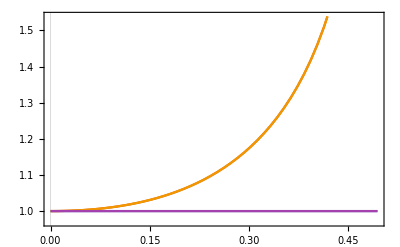

```mathematica
ListPlot[{{cs,D11winf}ᵀ,{cs,D11winfsmallc}ᵀ,{cs,D22winf}ᵀ,{cs,D22winfsmallc}ᵀ},Joined->True,PlotTheme->"Scientific"]
```

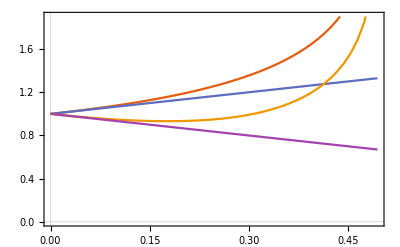

-Graphics-

```mathematica
i1=e1/.c->0//FullSimplify
i2=e2/.c->1//FullSimplify
```

(Q^2 Sin[p]^2 Sin[θr[r]]^2)/r^2+Cos[p]^2 θr'[r]^2

(Q^2 Cos[p]^2 Sin[θr[r]]^2)/r^2+Sin[p]^2 θr'[r]^2

```mathematica
e1/.c->0//FullSimplify
e2/.c->1//FullSimplify
```

(Q^2 Sin[p]^2 Sin[θr[r]]^2)/r^2+Cos[p]^2 θr'[r]^2

(Q^2 Cos[p]^2 Sin[θr[r]]^2)/r^2+Sin[p]^2 θr'[r]^2

```mathematica
Integrate[i1,{p,0,2π}]
Integrate[i2,{p,0,2π}]
```

π ((Q^2 Sin[θr[r]]^2)/r^2+θr'[r]^2)

π ((Q^2 Sin[θr[r]]^2)/r^2+θr'[r]^2)

```mathematica
Clear[R,w]
ir=Limit[(Q^2 Sin[θr[r]]^2)/r^2+θr'[r]^2/.θr->θsk,w->∞]
```

(4 (1+Q^2) R^2)/((r^2+R^2)^2)

```mathematica
Integrate[π ir r,{r,0,∞}]
```

ConditionalExpression[2 π (1+Q^2), Re[R]≠0]